## QSim` Documentation

### Preamble

QSim is a stand-alone package, and does not require other packages to run.

```mathematica
Needs["QSim`"]
```

The following packages are needed to run some code found in this documentation notebook.

```mathematica
Needs["DocTools`"]
Needs["Tensor`"]
```

### Source Code

Open Source Code

## Introduction and Overview

QSim` is a general purpose quantum system time-evolution simulator whose primary objective is ease of use. This is in keeping with one of Mathematica’s main advantages over most other languages; rapid and intuitive development of ideas with minimal overhead. A description of the the quantum system, usually a Hamiltonian, and an action on that quantum system are provided, and some observable, quantum state, propogator, etc. is monitored as the system evolves.

As a quick example, the following computes the expectation value of X⊗Y of the initial state |00⟩ undergoing evolution with the time-dependent Hamiltonian H(t)=cos(t)X⊗X+sin(t)Y⊗Y. Note that over half the code is for plotting and not for simulating -- it is really a one liner!

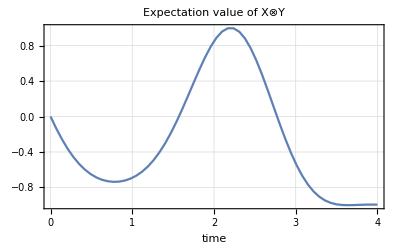

```mathematica
ListPlot[
Observables[EvalPulse[Cos[#]X⊗X+Sin[#]Y⊗Y&,4,PollingInterval->0.1,InitialState->Projector[{1,0,0,0}],Observables->{X⊗Y}],TimeVector->True],
Joined->True,PlotRange->All,PlotTheme->"Detailed",
PlotLabel->"Expectation value of X⊗Y",FrameLabel->{"time",None}
]
```

## EvalPulse

EvalPulse[H,p] simulates the pulse p under the Hamiltonian H. There are four types of “pulses” that p can be:

Type | Predicate | Description
Drift pulse | DriftPulseQ | Evolution under the Hamiltonian for some time. In this case, p is just equal to a number,or a Symbol such as t.
Shaped pulse | ShapedPulseQ | A list of control Hamiltonians,time spacings,and amplitudes is provided, and everything is simulated. In this case, 
p is of the form {pulse,{Hctl1,Hctl2,...}} where pulse is either a text file (eg. CVS) containing the shaped pulse, or the 
shaped pulse itself. A shaped pulse is of the form 
{{dt1,a11,a12,a13,...},{dt2,a21,a22,a23,...},{dt2,a21,a22,a23,...},...}.
Unitary pulse | UnitaryPulseQ | The Hamiltonian is ignored and some other unitary is applied. This kind of pulse only really makes within pulse sequences. 
In this case, p is of the form {U,t} where U is the unitary matrix and t is how much time the pulse should take.
Channel pulse | ChannelPulseQ | The Hamiltonian is ignored, and the supplied superoperator is applied. Similar to a unitary pulse, a superoperator pulse 
only really makes sense in the context of a pulse sequence. Also note that you cannot expect any unitaries to be 
returned from a simulation involving a superoperator pulse: it is required that an initial state be given with this kind of pulse.

The Hamiltonian can be time dependent or time independent. In the former case the Hamiltonian H is a matrix, and in the latter case, the Hamiltonian H is a single parameter function returning a matrix. Alternatively, the first argument of EvalPulse can not be a Hamiltonian at all, but rather a Lindblad representation, L=LindbladForm[H,L1,L2,...,Ln]. where H is time dependent or independent as described earlier, and L1,...,Ln are (time independent) Lindblad matrices.

Type | Predicate | Description
Time independent Hamiltonian | DriftHamConstQ | A matrix.
Time dependent Hamiltonian | DriftHamNonConstQ | A single parameter function returning a matrix.
Time independent Lindblad | LindbladConstQ | A Lindblad representation,L=LindbladForm[H,L1,L2,...,Ln], 
where H satisfies DriftHamConstQ.
Time dependent Lindblad | LindbladNonConstQ | A Lindblad representation,L=LindbladForm[H,L1,L2,...,Ln], 
where H satisfies DriftHamNonConstQ.

The particular simulator invoked by Evalpulse[H,p] depends on which predicates H and p satisfy.

### Options

Examples of these options being used appear in subsequent subsections.

Option | Default Value | Description
StepSize | Automatic | StepSize is a simulation option that chooses the time discretization when the internal Hamiltonian is time dependent. Can be set to Automatic.
PollingInterval | Off | PollingInterval is a simulation option that specifies the time interval at which results of the simulation should be returned. The default value is Off.
InitialState | None | InitialState is a simulation option. Set this option to the initial density matrix of your system. The default value is None.
Observables | None | Observables is three things: (1) simulation option which can be set to a list of observables (list of hermitian matrices), (2) an element of the SimulationOutput list, and (3) a function Observables[data] (Observables[data,n]) which extracts all observable values (n'th observable values) from data, where data is in the format that EvalPulse outputs.
Functions | None | Functions is three things: (1) simulation option which can be set to a list of functions which take a square matrix as input, (2) an element of the SimulationOutput list, and (3) a function Functions[data] (Functions[data,n]) which extracts all function values (n'th function values) from data, where data is in the format that EvalPulse outputs.
SimulationOutput | Automatic | SimulationOutput is a simulation option. Set this option to be one of, or a nonempty subset of, the list {Unitaries,States,Observables,Functions}. These will be the values (and order) of the simulation output. The default value is Automatic.
SequenceMode | False | SequenceMode is a simulation option. If set to True, EvalPulse returns the final state (or None) in addition to the usual output.
NumericEvaluation | True | NumericEvaluation is a simulation option. If set to True, N is called on all times inside MatrixExp, and if set to False, N is not called. The default value is True.
LindbladQ | False | LindbladQ[L] returns True iff one of DriftHamConstQ[L] or DriftHamNonConstQ[L] is True.

### Running a Simulation

Running a simulation is as easy as specifying a Hamiltonian and a pulse. Interpretting the output is discussed in the next section.

```mathematica
EvalPulse[X,1]
```

{{Unitaries,{{{1,0},{0,1}},{{0.540302+0. ⅈ,0.-0.841471 ⅈ},{0.-0.841471 ⅈ,0.540302+0. ⅈ}}}},{TimeVector,{0,1}}}

#### Numeric vs Symbolic Computation

By default, the option NumericEvaluation is True:

```mathematica
EvalPulse[X,1]
```

{{Unitaries,{{{1,0},{0,1}},{{0.540302+0. ⅈ,0.-0.841471 ⅈ},{0.-0.841471 ⅈ,0.540302+0. ⅈ}}}},{TimeVector,{0,1}}}

If set to False, EvalPulse will atempt to solve the system symbolically. This will of course only succeed in a reasonable amount of time for simple systems.

```mathematica
EvalPulse[X,t,NumericEvaluation->False]
```

{{Unitaries,{{{1,0},{0,1}},{{Cos[t],-ⅈ Sin[t]},{-ⅈ Sin[t],Cos[t]}}}},{TimeVector,{0,t}}}

### Simulation Output Format

As seen in the examples of the previous section, the output of EvalPulse is a list of types with corresponding data of the form {{Type1,data1},{Type2,data2},...}. The six types are:

Type | Data Description
TimeVector | A list of times  indexing the data of other types. The only type which is always output.
Unitaries | A list of unitary matrices, corresponding to the TimeVector times.
States | A list of density matrices, corresponding to the TimeVector times.
Functions | A list of function return values, corresponding to the TimeVector times.
Observables | A list observable values, corresponding to the TimeVector times.
Superoperators | A list of superoperator matrices, corresponding to the TimeVector times.

#### Polling Interval

The times at which the simulation is polled for output data can be changed with the option PollingData, which specifies an interval of time. The polling times are recorded in TimeVector. By default, the system is polled at two positions, time zero and the final time. Each of the other ouput types return a value for each polling time.

Important Note: The PollingInterval does not affect the resolution at which the system is simulated, it only affects the interval at which an output is demanded; PollingInterval is completely unrelated to the StepSize of a time dependent Hamiltonian, or the pulse widths of a ShapedPulseQ. These times need not be even multiples of each other.

```mathematica
EvalPulse[X,1,PollingInterval->0.1]
```

{{Unitaries,{{{1,0},{0,1}},{{0.995004+0. ⅈ,0.-0.0998334 ⅈ},{0.-0.0998334 ⅈ,0.995004+0. ⅈ}},{{0.980067+0. ⅈ,0.-0.198669 ⅈ},{0.-0.198669 ⅈ,0.980067+0. ⅈ}},{{0.955336+0. ⅈ,0.-0.29552 ⅈ},{0.-0.29552 ⅈ,0.955336+0. ⅈ}},{{0.921061+0. ⅈ,0.-0.389418 ⅈ},{0.-0.389418 ⅈ,0.921061+0. ⅈ}},{{0.877583+0. ⅈ,0.-0.479426 ⅈ},{0.-0.479426 ⅈ,0.877583+0. ⅈ}},{{0.825336+0. ⅈ,0.-0.564642 ⅈ},{0.-0.564642 ⅈ,0.825336+0. ⅈ}},{{0.764842+0. ⅈ,0.-0.644218 ⅈ},{0.-0.644218 ⅈ,0.764842+0. ⅈ}},{{0.696707+0. ⅈ,0.-0.717356 ⅈ},{0.-0.717356 ⅈ,0.696707+0. ⅈ}},{{0.62161+0. ⅈ,0.-0.783327 ⅈ},{0.-0.783327 ⅈ,0.62161+0. ⅈ}},{{0.540302+0. ⅈ,0.-0.841471 ⅈ},{0.-0.841471 ⅈ,0.540302+0. ⅈ}}}},{TimeVector,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}}}

#### Default Output Types

The (non-TimeVector) output types returned by a given simulation are by default chosen automatically using common sense rules:
	| If no InitialState or Functions options are given, Unitaries is the only output type
	| If InitialState is given as an option, but neither Observables nor Functions is, States is the only output type
	| If InitialState is given as an option, and either of Observables or Functions is also, Observables or Functions will be the output type
	| If Unitaries was supposed to be an automatic output type but the evolution was not pure (e.g. using LindbladForm) Superoperators will be the return type.

```mathematica
EvalPulse[X,1]
EvalPulse[X,1,InitialState->UP]
```

{{Unitaries,{{{1,0},{0,1}},{{0.540302+0. ⅈ,0.-0.841471 ⅈ},{0.-0.841471 ⅈ,0.540302+0. ⅈ}}}},{TimeVector,{0,1}}}

{{States,{{{1,0},{0,0}},{{0.291927+0. ⅈ,0.+0.454649 ⅈ},{0.-0.454649 ⅈ,0.708073+0. ⅈ}}}},{TimeVector,{0,1}}}

#### Manual Selection of Ouput Types

Use the option SimulationOutput to force certain output types (TimeVector is always included):

```mathematica
EvalPulse[X,1,InitialState->{{1,0},{0,0}},SimulationOutput->{States,Unitaries}]
```

{{States,{{{1,0},{0,0}},{{0.291927+0. ⅈ,0.+0.454649 ⅈ},{0.-0.454649 ⅈ,0.708073+0. ⅈ}}}},{Unitaries,{{{1,0},{0,1}},{{0.540302+0. ⅈ,0.-0.841471 ⅈ},{0.-0.841471 ⅈ,0.540302+0. ⅈ}}}},{TimeVector,{0,1}}}

#### Parsing Output Data

To extract one of the data objects from a simulation output {{Type1,data1},{Type2,data2},...}, the given type Head can be used: Type2[{{Type1,data1},{Type2,data2},...}].

For example, if we want to extract the unitary matrices from a simulation, we can do as follows:

```mathematica
outputdata=EvalPulse[X,1,PollingInterval->0.1];
Unitaries[outputdata]
```

{{{1,0},{0,1}},{{0.995004+0. ⅈ,0.-0.0998334 ⅈ},{0.-0.0998334 ⅈ,0.995004+0. ⅈ}},{{0.980067+0. ⅈ,0.-0.198669 ⅈ},{0.-0.198669 ⅈ,0.980067+0. ⅈ}},{{0.955336+0. ⅈ,0.-0.29552 ⅈ},{0.-0.29552 ⅈ,0.955336+0. ⅈ}},{{0.921061+0. ⅈ,0.-0.389418 ⅈ},{0.-0.389418 ⅈ,0.921061+0. ⅈ}},{{0.877583+0. ⅈ,0.-0.479426 ⅈ},{0.-0.479426 ⅈ,0.877583+0. ⅈ}},{{0.825336+0. ⅈ,0.-0.564642 ⅈ},{0.-0.564642 ⅈ,0.825336+0. ⅈ}},{{0.764842+0. ⅈ,0.-0.644218 ⅈ},{0.-0.644218 ⅈ,0.764842+0. ⅈ}},{{0.696707+0. ⅈ,0.-0.717356 ⅈ},{0.-0.717356 ⅈ,0.696707+0. ⅈ}},{{0.62161+0. ⅈ,0.-0.783327 ⅈ},{0.-0.783327 ⅈ,0.62161+0. ⅈ}},{{0.540302+0. ⅈ,0.-0.841471 ⅈ},{0.-0.841471 ⅈ,0.540302+0. ⅈ}}}

### Functions and Observables

In addition to tracking States and Unitaries of a system as it evolves, EvalPulse can also track Observables and Functions.

#### Observables

Observables as an option to EvalPulse should be a list of matrices {A_1,A_2,...,A_n}, each the same dimension as your Hamiltonian. An InitialState is required to use Observables. At each PollingInterval, the expression a_i(t)=Tr(ρ(t).A_i) is computed for each 1⩽i⩽n, where ρ(t) is the state of the system at the time t. The output data for Observables is therefore of the form {{a_1(t_0),a_2(t_0),...,a_n(t_0)},{a_1(t_0),a_2(t_0),...,a_n(t_0)},...}.

```mathematica
outputdata=EvalPulse[X,1,PollingInterval->0.1,InitialState->UP,Observables->{Y,Z}]
```

{{Observables,{{0,1},{-0.198669,0.980067},{-0.389418,0.921061},{-0.564642,0.825336},{-0.717356,0.696707},{-0.841471,0.540302},{-0.932039,0.362358},{-0.98545,0.169967},{-0.999574,-0.0291995},{-0.973848,-0.227202},{-0.909297,-0.416147}}},{TimeVector,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}}}

Output Observables data can be collected with Observables. Note that the data is transposed to make it easier to plot.

```mathematica
Observables[outputdata]
```

{{0,-0.198669,-0.389418,-0.564642,-0.717356,-0.841471,-0.932039,-0.98545,-0.999574,-0.973848,-0.909297},{1,0.980067,0.921061,0.825336,0.696707,0.540302,0.362358,0.169967,-0.0291995,-0.227202,-0.416147}}

Note that the TimeVector option adds corresponding times to the data:

```mathematica
Observables[outputdata,TimeVector->True]
```

{{{0,0},{1/10,-0.198669},{1/5,-0.389418},{3/10,-0.564642},{2/5,-0.717356},{1/2,-0.841471},{3/5,-0.932039},{7/10,-0.98545},{4/5,-0.999574},{9/10,-0.973848},{1,-0.909297}},{{0,1},{1/10,0.980067},{1/5,0.921061},{3/10,0.825336},{2/5,0.696707},{1/2,0.540302},{3/5,0.362358},{7/10,0.169967},{4/5,-0.0291995},{9/10,-0.227202},{1,-0.416147}}}

#### Functions

Functions as an option to EvalPulse should be a list of functions {f_1,f_2,...,f_n}. At each PollingInterval, if an InitialState was entered, the expression a_i(t)=f_i(ρ(t)) is computed for each 1⩽i⩽n, where ρ(t) is the state of the system at the time t, and if an Initial state was not entered, the expression a_i(t)=f_i(U(t)) is computed for each 1⩽i⩽n, where U(t) is the unitary propagator matrix of the system at the time t. The output data for Functions is therefore of the form {{a_1(t_0),a_2(t_0),...,a_n(t_0)},{a_1(t_0),a_2(t_0),...,a_n(t_0)},...}. Note that the ouput format of the functions need not be a scalar; it can be anything, unlike the examples below.

```mathematica
outputdata=EvalPulse[X,1,PollingInterval->0.1,Functions->{Re@Tr[#.#]&,First[Eigenvalues[#,1]]&}]
```

{{Functions,{{2,1},{1.96013,0.995004-0.0998334 ⅈ},{1.84212,0.980067-0.198669 ⅈ},{1.65067,0.955336-0.29552 ⅈ},{1.39341,0.921061+0.389418 ⅈ},{1.0806,0.877583-0.479426 ⅈ},{0.724716,0.825336-0.564642 ⅈ},{0.339934,0.764842-0.644218 ⅈ},{-0.058399,0.696707-0.717356 ⅈ},{-0.454404,0.62161+0.783327 ⅈ},{-0.832294,0.540302-0.841471 ⅈ}}},{TimeVector,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}}}

Output Functions data can be collected with Functions. Note that the data is transposed to make it easier to plot.

```mathematica
Functions[outputdata]
```

{{2,1.96013,1.84212,1.65067,1.39341,1.0806,0.724716,0.339934,-0.058399,-0.454404,-0.832294},{1,0.995004-0.0998334 ⅈ,0.980067-0.198669 ⅈ,0.955336-0.29552 ⅈ,0.921061+0.389418 ⅈ,0.877583-0.479426 ⅈ,0.825336-0.564642 ⅈ,0.764842-0.644218 ⅈ,0.696707-0.717356 ⅈ,0.62161+0.783327 ⅈ,0.540302-0.841471 ⅈ}}

Note that the TimeVector option adds corresponding times to the data:

```mathematica
Functions[outputdata,TimeVector->True]
```

{{{0,2},{1/10,1.96013},{1/5,1.84212},{3/10,1.65067},{2/5,1.39341},{1/2,1.0806},{3/5,0.724716},{7/10,0.339934},{4/5,-0.058399},{9/10,-0.454404},{1,-0.832294}},{{0,1},{1/10,0.995004-0.0998334 ⅈ},{1/5,0.980067-0.198669 ⅈ},{3/10,0.955336-0.29552 ⅈ},{2/5,0.921061+0.389418 ⅈ},{1/2,0.877583-0.479426 ⅈ},{3/5,0.825336-0.564642 ⅈ},{7/10,0.764842-0.644218 ⅈ},{4/5,0.696707-0.717356 ⅈ},{9/10,0.62161+0.783327 ⅈ},{1,0.540302-0.841471 ⅈ}}}

### Plotting Simulation Results

### Time Dependent Hamiltonians

### Lindbladians

### Implementation Details

## EvalPulseSequence

## EvalPulseOverDist